## Example: Double Sheet

### Lattice

```mathematica
L=1;
Λ1 = Flatten[Table[{i, j, 0}, {i, -L, L},{j,-L,  L}],1];
Λ2= Flatten[Table[{i, j, 1}, {i, -L, L},{j,-L,  L}],1];
Λ = Union[Λ1,Λ2]
λ = Length[Λ];
```

{{-1,-1,0},{-1,-1,1},{-1,0,0},{-1,0,1},{-1,1,0},{-1,1,1},{0,-1,0},{0,-1,1},{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,-1,0},{1,-1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1}}

```mathematica
FullGraphics[ListPointPlot3D[Λ,PlotStyle->{Blue,PointSize[0.05]}, Axes-> False, PlotRange->Full]]
```

FullGraphics[-Graphics3D-]

### Interaction Tensors

#### Dipole Interaction

```mathematica
Simplify[({{1/2, -I/2, 0}, {1/2, I/2, 0}, {0, 0, 1}}).({{1/2, 1/2, 0}, {-I/2, I/2, 0}, {0, 0, 1}})]//MatrixForm
```

(0 | 1/2 | 0
1/2 | 0 | 0
0 | 0 | 1)

```mathematica
Simplify[({{1/2, -I/2, 0}, {1/2, I/2, 0}, {0, 0, 1}}).({{3 dx^2- r^2, 3dy dx, 3 dz dx}, {3dx dy, 3 dy^2- r^2, 3dy dz}, {3dx dz, 3dy dz, 3 dz^2- r^2}}).({{1/2, 1/2, 0}, {-I/2, I/2, 0}, {0, 0, 1}})]//MatrixForm
```

(3/4 (dx-ⅈ dy)^2 | 1/4 (3 dx^2+3 dy^2-2 r^2) | 3/2 (dx-ⅈ dy) dz
1/4 (3 dx^2+3 dy^2-2 r^2) | 3/4 (dx+ⅈ dy)^2 | 3/2 (dx+ⅈ dy) dz
3/2 (dx-ⅈ dy) dz | 3/2 (dx+ⅈ dy) dz | 3 dz^2-r^2)

```mathematica
a=1;
b=1;
c=2.27;
LS = {{a, 0, 0}, {0, b, 0}, {0, 0, c}};
Ja=-29.20;
Jb=-29.20;
Jc=0.43;
Ds =0.54;
(*spin-spin exchange interaction*)
V1[v1_,v2_, s1_, s2_]:=Module[{r, dx, dy, dz},
r = Norm[(v1-v2)];
If[r!=1,Return[0] ];
dx= Norm[(v1-v2)[[1]]];
If[dx==1, If[(s1==1&&s2==2) || (s1==2 && s2==1) , Return[Ja/2], If[s1==3&&s2==3, Return[Ja]]]];
dy= Norm[(v1-v2)[[2]]];
If[dy==1, If[(s1==1&&s2==2) || (s1==2 && s2==1) , Return[Jb/2], If[s1==3&&s2==3, Return[Jb]]]];
dz= Norm[(v1-v2)[[3]]];
If[dz==1, If[(s1==1&&s2==2) || (s1==2 && s2==1) , Return[Jc/2], If[s1==3&&s2==3, Return[Jc]]]];
Return[0];
]
(*dipoloe interaction*)
V2[v1_, v2_, s1_, s2_]:=Module[{r, dx, dy, dz},
If[v1==v2, Return[0]];
r = Norm[LS.(v1-v2)];
dx= (LS. v1-v2)[[1]];
dy= (LS. v1-v2)[[2]];
dz= (LS. v1-v2)[[3]];
If[s1==1&&s2==1, Return[3/4 Ds (dx-ⅈ dy)^2/r^5]];
If[s1==1&&s2==2, Return[1/4 Ds(3 dx^2+3 dy^2-2 r^2)/r^5]];
If[s1==1&&s2==3, Return[3/2 Ds(dx-ⅈ dy) dz/r^5]];
If[s1==2&&s2==1, Return[1/4 Ds(3 dx^2+3 dy^2-2 r^2)/r^5]];
If[s1==2&&s2==2, Return[3/4 Ds(dx+ⅈ dy)^2/r^5]];
If[s1==2&&s2==3, Return[3/2 Ds (dx+ⅈ dy) dz/r^5]];
If[s1==3&&s2==1, Return[3/2 Ds(dx-ⅈ dy) dz/r^5]];
If[s1==3&&s2==2, Return[3/2 Ds(dx+ⅈ dy) dz/r^5]];
If[s1==3&&s2==3, Return[Ds(3 dz^2-r^2)/r^5]];
Return[0];
]
V[v1_, v2_, s1_, s2_]:= V1[v1, v2, s1, s2]+V2[v1, v2, s1, s2];
```

```mathematica
Table[V[{0,0,0}, {1, 4, 0}, i, j],{i, 1, 3}, {j, 1, 3} ]//MatrixForm//N
```

(-0.0000776261-0.0000414006 ⅈ | -0.000312229 | 0.
-0.000312229 | -0.0000776261+0.0000414006 ⅈ | 0.
0. | 0. | -0.000800411)

### Correlation Function: dipole, Sz

```mathematica
acc = 1;
vIndex= 9;
sIndex=3;(*Subscript[S, z] spin operator*)
t=0;
```

```mathematica
ZT = Table[{T, Z[acc,1/T]}, {T, 10, 11, .2}];
```

```mathematica
OzTun = Table[OnePoint[acc,1/T, vIndex, sIndex, t], {T, 10, 11, .2}];
```

```mathematica
OzT= Table[{ZT[[k]][[1]],OzTun[[k]]/ZT[[k]][[2]]}, {k, 1, Length[ZT]}];
```

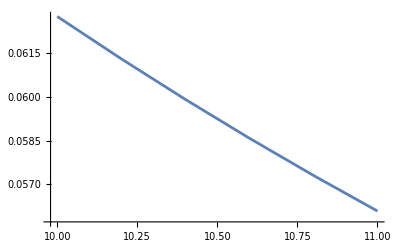

```mathematica
ListPlot[OzT, Joined->True]
```

### Correlation Function: dipole, Sx and Sy

```mathematica
(*S_+ = Subscript[S, x]+I Subscript[S, y]; S_- = Subscript[S, x] - I Subscript[S, y]*)
```

```mathematica
acc = 1;
vIndex= 9;
sIndex1=1;
sIndex2 =2;
t=0;
```

```mathematica
ZT = Table[{T, Z[acc,1/T]}, {T, 10, 11, .2}];
```

```mathematica
OpTun = Table[OnePoint[acc,1/T, vIndex, sIndex1, t], {T, 10, 11, .2}];
```

```mathematica
OmTun = Table[OnePoint[acc,1/T, vIndex, sIndex2, t], {T, 10, 11, .2}];
```

```mathematica
OxT= Table[{ZT[[k]][[1]],(OpTun[[k]] + OmTun[[k]] )/(2ZT[[k]][[2]])}, {k, 1, Length[ZT]}]//Chop
OyT= Table[{ZT[[k]][[1]],(-I)(OpTun[[k]] - OmTun[[k]] )/(2ZT[[k]][[2]])}, {k, 1, Length[ZT]}]//Chop
```

{{10.,0},{10.2,0},{10.4,0},{10.6,0},{10.8,0},{11.,0}}

{{10.,0},{10.2,0},{10.4,0},{10.6,0},{10.8,0},{11.,0}}

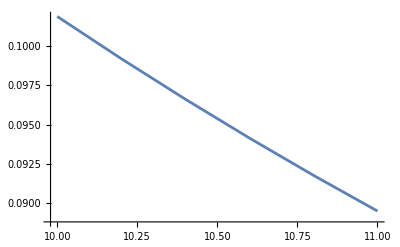

```mathematica
ListPlot[OzT, Joined->True]
```